# Vaje iz Mathematice

Rešuj naloge v celicah med navodili. Pomagaj si z gradivom na spletni učilnici.

1. naloga: Izračunaj vrednost izraza ((20 +316)^7-55)/(33 12)^3. Izračunaj tudi numerično vrednost izraza na 20 mest natančno.

```mathematica
izraz=((20+316)^7-55)/(33 12)^3
```

483476023799709641/62099136

```mathematica
N[izraz,20]
```

7.7855515381036805568×10^9

```mathematica
N[Pi,50]
```

3.1415926535897932384626433832795028841971693993751

2. naloga: Poenostavi izraz 2^x+5 a 2^x+2^(x+2). Pomagaj si z ukazom Simplify.

```mathematica
Simplify[2^x+5 a 2^x+2^(x+2)]
```

5 2^x (1+a)

3. naloga: Izračunaj 30! - 20!. Kakšna je 10 števka od leve proti desni? Razcepi rezultat na prafaktorje. Katero je največje praštevilo v razcepu? Katero praštevilo nastopa v razcepu z najvišjo potenco.

```mathematica
izraz1=30!-20!
```

265252859812188625734300303360000

```mathematica
seznam=IntegerDigits[izraz1]
```

{2,6,5,2,5,2,8,5,9,8,1,2,1,8,8,6,2,5,7,3,4,3,0,0,3,0,3,3,6,0,0,0,0}

```mathematica
IntegerDigits[izraz1][[10]]
```

8

```mathematica
seznam[[10]]
```

8

```mathematica
(*10ta od desne proti levi*)
Reverse[seznam][[10]]
```

0

```mathematica
FactorInteger[izraz1]
```

{{2,18},{3,8},{5,4},{7,2},{11,1},{13,1},{17,1},{19,1},{124669,1},{874534571,1}}

```mathematica
Divisors[izraz1]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,164122,13960676832220453986015805440000,14736269989566034763016683520000,15603109400716977984370606080000,16578303738261789108393768960000,17683523987479241715620020224000,18946632843727758981021450240000,20404066139399125056484638720000,22104404984349052144525025280000,24113896346562602339481845760000,26525285981218862573430030336000,29472539979132069526033367040000,33156607476523578216787537920000,37893265687455517962042900480000,44208809968698104289050050560000,53050571962437725146860060672000,66313214953047156433575075840000,88417619937396208578100101120000,132626429906094312867150151680000,265252859812188625734300303360000}
 |  |  |  |

4. naloga: Poišči največji skupni delitelj in najmanjši skupni večkratnik števil: 536, 1248, 2320.

```mathematica
GCD[536,1248,2320]
```

8

```mathematica
LCM[536,1248,2320]
```

12124320

5. naloga: Izračunaj vrednost izraza (x^5- 2 x^2+3x + 4)/(x^5-2x - 1) pri x = 1, 2, 3, 4. Uporabi ustrezna transformacijska pravila in ukaz ReplaceAll (oz /.)

```mathematica
(x^5-2 x^2+3 x+4)/(x^5-2 x-1)/.x->{1,2,3,4}
```

{-3,34/27,119/118,144/145}

6. naloga: Napiši funkcijo odvisno od x, katere vrednost je ravno izraz iz prejšnje naloge. S pomočjo ukaza Table izračunaj vrednosti funkcije v točkah od 1 do 10.

```mathematica
Table[1,5]
```

{1,1,1,1,1}

```mathematica
Table[i,{i,5}]
```

{1,2,3,4,5}

```mathematica
Table[i,{i,-5,5, 2}](*korak 2 na koncu!!!*)
```

{-5,-3,-1,1,3,5}

```mathematica
(x^5-2 x^2+3 x+4)/(x^5-2 x-1)/.x->Table[i,{i,10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
ClearAll[f]
```

```mathematica
f[x_]:=(x^5-2 x^2+3 x+4)/(x^5-2 x-1)
```

```mathematica
Table[f[i],{i,10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
Table[f[i],{i,1,10,0.5}](*korak 0,5 od 1 do 10*)
```

{-3.,3.22609,1.25926,1.05455,1.00847,0.996133,0.993103,0.992917,0.993577,0.994423,0.995234,0.995944,0.996546,0.997048,0.997466,0.997813,0.998103,0.998345,0.99855}

```mathematica
t=Table[i,{i,0,10}]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Mean[t]
Min[t]
Max[t]
Total[t]
```

5

0

10

55

```mathematica
Take[t,3]
Take[t,-3]
Drop[t,3]
```

{0,1,2}

{8,9,10}

{3,4,5,6,7,8,9,10}

```mathematica
t[[2;;4;;2]](*tabela od 2. do 4. el. s korakom 2*)
```

{1,3}

7. naloga: Izračunaj naslednje limite:
	lim_(x→ 2) (x^3- 4 x^2+2x + 4)/(x^5-9x - 14)
	lim_(x→ 0) (arctan(7x))/(arcsin(8x))
	lim_(x→ 5) (x^2-25)cot(πx)
	lim_(x→ π) (1 + cos x)/(2 √πx- π - x)
	lim_(x→ 0^+) |x| cot x
lim_(x→ 0^-) |x| cot x

```mathematica
Limit[(x^3-4 x^2+2 x+4)/(x^5-9 x-14),x->2]
```

-2/71

```mathematica
Limit[(1+Cos [x])/(2 Sqrt[Pi x]-Pi-x),x->Pi]
```

-2 π

```mathematica
(+leva limita direction 1*)
```

```mathematica
Limit[Abs[x]*Cot[x], x->0, Direction->1]
Limit[Abs[x]*Cot[x], x->0, Direction->-1]
```

-1

1

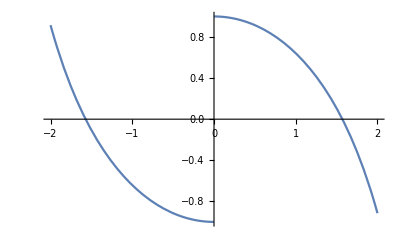

```mathematica
Plot[Abs[x]*Cot[x], {x,-2,2}]
```

8. naloga: Izračunaj odvode naslednjih funkcij:
	y = (arctan(x))/(arcsin(x))
	y = (((x^3 + 1)^(1/3) + 5)/(4 (x^3+1)^(1/3)+2))^(2/5)
	y = √((x^2 + 1)^(1/3) +(x^2 + 1)^(1/4))  
	y = (x + 1)^x

```mathematica
D[(ArcTan[x])/(ArcSin[x]),x]
```

1/((1+x^2) ArcSin[x])-ArcTan[x]/(√(1-x^2) ArcSin[x]^2)

```mathematica
D[(x+1)^x,x]
```

(1+x)^x (x/(1+x)+Log[1+x])

9. naloga: Seštej vsa soda števila na intervalu od [1, 100].

```mathematica
ClearAll[t]
```

```mathematica
t=Table[i,{i,2,100,2}]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100}

```mathematica
Total[t]
```

2550

```mathematica
Sum[2i,{i,1,50}]
```

2550

10. naloga: Izračunaj ∑_(k=1)^∞ (k^2+1)/k^4.

```mathematica
Sum[(k^2+1)/k^4,{k,1,Infinity}]
```

1/90 π^2 (15+π^2)

11. naloga: S pomočjo implicitnega odvajanja izračunaj odvode y'(x). Za prvi primer si oglej zgled spodaj.
	cos√xy= x^2 y^2+ 1 
	1 + sin(xy) = tan(x + y)
	tan^2(x + y)= x^2y^2 - 3

```mathematica
odvod  = D[Cos[Sqrt[x y[x]]]== x^2 (y[x])^2 + 1,  x]
resitev =First[Solve[odvod, y'[x]]]
y'[x] /. resitev
```

-(Sin[√(x y[x])] (y[x]+x y'[x]))/(2 √(x y[x]))==2 x y[x]^2+2 x^2 y[x] y'[x]

{y'[x]→-y[x]/x}

-y[x]/x

12. naloga: Eksaktno izračunaj ničle polinoma  -1+2 x-7 x^2+x^3.

```mathematica
Solve[-1+2 x-7 x^2+x^3==0,x]
```

{{x→1/3 (7+(587/2-(3 √2949)/2)^(1/3)+(1/2 (587+3 √2949))^(1/3))},{x→7/3-1/6 (1+ⅈ √3) (587/2-(3 √2949)/2)^(1/3)-1/6 (1-ⅈ √3) (1/2 (587+3 √2949))^(1/3)},{x→7/3-1/6 (1-ⅈ √3) (587/2-(3 √2949)/2)^(1/3)-1/6 (1+ⅈ √3) (1/2 (587+3 √2949))^(1/3)}}

```mathematica
polinom=-1+2 x-7 x^2+x^3
```

-1+2 x-7 x^2+x^3

```mathematica
Factor[x ^2-1]
```

(-1+x) (1+x)

```mathematica
FactorList[polinom]
```

{{1,1},{-1+2 x-7 x^2+x^3,1}}

```mathematica
FactorList[x^2-1]
```

```mathematica
{{1,1},{-1+x,1},{1+x,1}}(*enkrat,enkrat potem linearni polinom in stopnja*)
```

```mathematica
Expand[(x+1)*x^2]
```

x^2+x^3

```mathematica
PolynomialGCD[x^2-1, x+1]
```

1+x

```mathematica
PolynomialQuotient[x^2-1, x+1,x](+ rabš x nakonc,da veš po čem deli*)
```

-1+x

13. naloga: Numerično izračunaj ničle polinoma 1-x+12 x^2-2 x^4+x^5. Koliko ničel je realnih? Kakšna je največja absolutna vrednost ničle. S pomočjo ukaza ReplaceAll  (oz. /.) uporabi seznam rešitev na simbolu x. Tako dobiš seznam vrednosti ničel. Nato s pomočjo ukaza Table, ukaza Part (oz [[  ]]) in ukaza Abs sestavi seznam absolutnih vrednosti. Na koncu na seznamu uporabi še funkcijo Max, ki vrne maksimum seznama.

```mathematica
prepPravila = NSolve[1-x+12 x^2-2 x^4+x^5,x]
```

{{x→-1.83104},{x→0.0403843-0.284163 ⅈ},{x→0.0403843+0.284163 ⅈ},{x→1.87514-1.76448 ⅈ},{x→1.87514+1.76448 ⅈ}}

```mathematica
nicle = x/.prepPravila
```

{-1.83104,0.0403843-0.284163 ⅈ,0.0403843+0.284163 ⅈ,1.87514-1.76448 ⅈ,1.87514+1.76448 ⅈ}

```mathematica
nicle
```

{-1.83104,0.0403843-0.284163 ⅈ,0.0403843+0.284163 ⅈ,1.87514-1.76448 ⅈ,1.87514+1.76448 ⅈ}

14. naloga: Razcepi polinom na linearne in kvadratne faktorje -1056+256 x-826 x^2+175 x^3+232 x^4-80 x^5+2 x^6+x^7.

15. naloga: Zmnoži polinom tako da dobiš vsoto monomov (x^2 (-1+y)-x^3 y^5+(-1+x)^7 x y (x^2+2 x y+y^3))^2.  Nato razvij polinom po potencah x (koeficienti so polinomi v y). Ugotovi najvišjo potenco n spremenljivke x, ki se pojavi v polinomu in izračunaj n-ti odvod polinoma.

16. naloga: Nariši graf funkcije y = (x^2 - 1)/(x^2- 4). Računsko pa pri tem določi (in se potem s sliko prepričaj) naslednje:
- ničle funkcije
- pole funkcije in obnašanje funkcije v okolicah polov
- asimptote
- ekstreme 
- prevoje
- intervale konveksnosti in konkavnosti
Rezultate naloge komentiraj z vmesnimi tekstovnimi celicami.

17. naloga: Analiziraj funkcijo y = arctanx^2/(x^2-1). Upoštevaj navodila iz prejšnje naloge.

18. naloga: Določi tangento na funkcijo y=sin^2 x-cos x v točki (2,y[2]). Rezultat predstavi s sliko.

19. naloga: Dana sta vektorja v1 = (1,2,3) in v2 = (-3,-2,5). Izračunaj njun skalarni produkt ter vektorski produkt. Kateri od vektorjev je daljši. Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

Izračunaj determinanto matrike.
M = (9 | 2 | -3
3 | 2 | 1
6 | 4 | -1)
Izračunaj tudi lastne vrednosti in lastne vektorje matrike M. Ali je matrika diagonalizabilna? Konstruiraj diagonalno matriko, prehodno matriko in njen inverz. Preveri, če produkt teh treh matrik da spet matriko M.

20. naloga: Dana je parametrično podana krivulja (((3-t) sin t)/(1+t),cos(t) sin(2 t)) za t ∈ [0,5]. Krivulja samo sebe preseka natanko dvakrat. S pomočjo numeričnega reševanja enačb (FindRoot) poišči približka koordinat točk. Sistem enačb nastavi tako da izenačiš par koordinat krivulj prametriziran s t s parom parametriziranim s spremenljivko s. Potem s spreminjanjem začetnih približkov poskusi določiti vrednosti parametra, pri katerih pride do samopresečič. Ko izračunaš točke p1, p2, ..., sestavi iz njih grafični objekt Graphics[{Point[p1], Point[p2], ...}] in ga z ukazom Show prikaži skupaj s sliko, ki jo pridela ukaz ParametricPlot. S tem grafično preveri, če gre za pravilen izračun.

21. naloga: S simboličnim računom dokaži identiteto a × (b × c) = b(a · c) − c(a · b) na trorazsežnih vektorjih.